```mathematica
myAxesSize=15;
myLabelSize=12;
myImageSize=600;
SetDirectory[NotebookDirectory[]];
```

## Get data

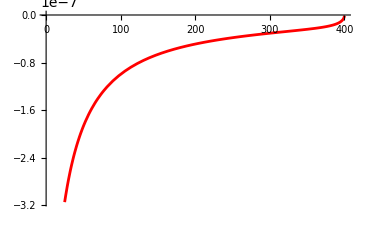

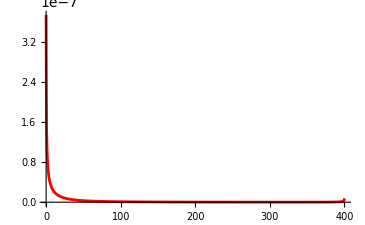

```mathematica
filename="wann/build/postprocdata.txt";
myfile=Import[filename,"Table"];
pressurepts=myfile[[;;,{1,2}]];
qpts=myfile[[;;,{1,3}]];
wellR=myfile[[1,4]];
fq=Interpolation[qpts,InterpolationOrder->1];
dfq=D[fq[x],x];
a=Plot[fq[x],{x,0,400},PlotStyle->Red]
a=Plot[dfq,{x,0,400},PlotStyle->Red,PlotRange->All]
b=ListPlot[qpts];
Show[a,b];
```

## Plot

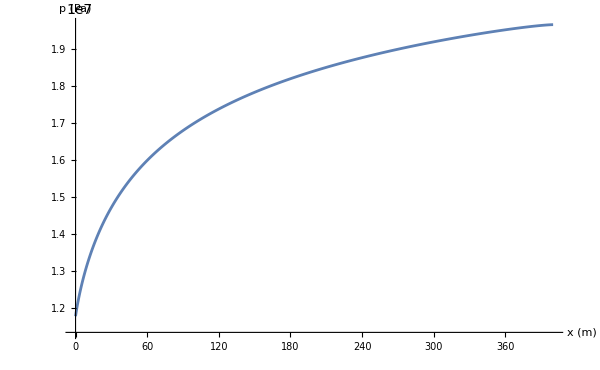

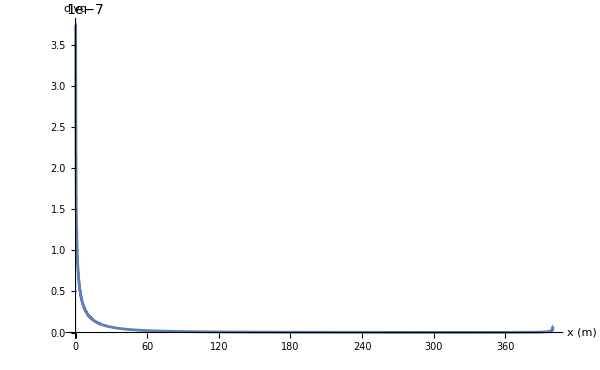

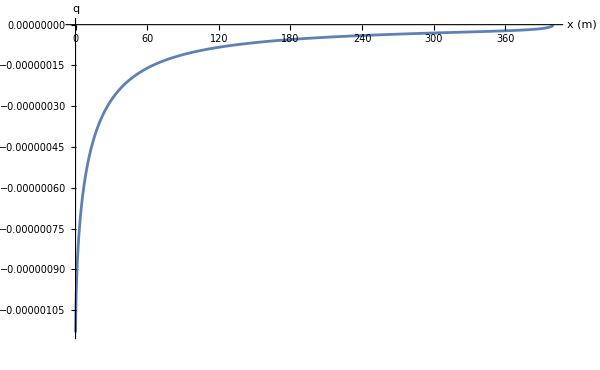

```mathematica
ListPlot[pressurepts,Joined->True,PlotRange->All,ImageSize->myImageSize,AxesLabel->{Style["x (m)",myAxesSize,Black],Style["p (Pa)",myAxesSize,Black]},LabelStyle->Directive[myLabelSize,Bold,Black]]
Plot[dfq,{x,0,400},PlotRange->All,ImageSize->myImageSize,AxesLabel->{Style["x (m)",myAxesSize,Black],Style["divq",myAxesSize,Black]},LabelStyle->Directive[myLabelSize,Bold,Black],PlotPoints->200]
ListPlot[qpts,Joined->True,PlotRange->All,ImageSize->myImageSize,AxesLabel->{Style["x (m)",myAxesSize,Black],Style["q",myAxesSize,Black]},LabelStyle->Directive[myLabelSize,Bold,Black]]
```

## Resistivity K

```mathematica
(*Max[Kpts[[;;,2]]] old value*)
```

```mathematica
Khw=(2π 10^-13)/(0.005 (2400/1));
pff=22064967.11;
npts=4001;
l=400.;
gap=l/(npts-1)
stride=Round[gap/(l/(Length[pressurepts]-1))]
xpts=Table[(i-1)gap,{i,npts}];
qlpts=Table[(dfq/.x->xpts[[i]]),{i,npts}];
ppts=Table[pressurepts[[1+(i-1)stride,2]],{i,npts}];
Kpts=Table[{(xpts[[i]]-l/2)/l 2,(-qlpts[[i]])/(ppts[[i]]-pff) } ,{i,npts}];
KptsNormalized=Table[{(xpts[[i]]-l/2)/l 2,wellR,(-qlpts[[i]])/(ppts[[i]]-pff) /Khw} ,{i,npts}];
(*ListPlot[KptsNormalized,Joined->True,PlotMarkers->Automatic,PlotRange->All,ImageSize->myImageSize,AxesLabel->{Style["x (m)",myAxesSize,Black],Style["K",myAxesSize,Black]},LabelStyle->Directive[myLabelSize,Bold,Black]]*)
(*Export["kpts.txt",KptsNormalized,"Table"]*)
file=OpenAppend["kpts.txt"];
Export[file,KptsNormalized,"Table"];
WriteString[file,"","\n"];
(*Write[file,KptsNormalized,"Table"];*)
Close[file];

KBCs={};
AppendTo[KBCs,KptsNormalized[[1]]];
AppendTo[KBCs,KptsNormalized[[-1]]];
filebc=OpenAppend["kpts_bc.txt"];
Export[filebc,KBCs,"Table"];
WriteString[filebc,"","\n"];
Close[filebc];
```

0.1

1

Piecewise[{{1.12447-0.00899577 z, 2 z>125}, {0.499084+0.00101043 z, True}}]

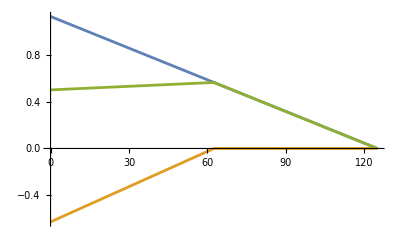

```mathematica
W=125; (*m*)
ρw=1020; (*kg/m^3*)
ρi=917; (*kg/m^3*)
g=9.81; (*m/s^2*)
pice=10^-6 ρi g (W-z);
pwater=If[z>W/2,0,-10^-6 ρw g (W/2-z)];
pres=pice+pwater//Simplify
Plot[{pice,pwater,pres},{z,0,W}]
```

```mathematica
f=Piecewise[{{1.12447125-0.00899577 z, z>125/2}, {0.49908374999999994+0.0010104300000000014 z, True}}]
```

Piecewise[{{1.12447-0.00899577 z, z>125/2}, {0.499084+0.00101043 z, True}}]

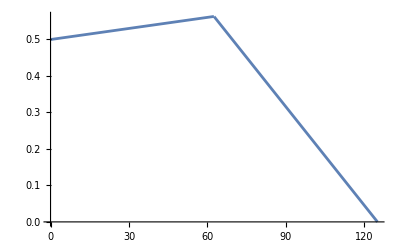

```mathematica
Plot[f,{z,0,W}]
```